```mathematica
ClearAll["Global`*"]
SetDirectory["/Users/baker/My Documents/06_06_2013/2ND_CAV/TAPER/SMOOTHING_OFF/HE"];
fname="c2.S1P";

file=Drop[Import[fname,"Table"],6];
dataraw=file;
data=dataraw;
f=ToExpression[data[[All,1]]];
S11RE=ToExpression[data[[All,2]]];
S11IM=ToExpression[data[[All,3]]];
S11Abs=Table[Abs[S11RE[[x]]+ⅈ S11IM[[x]]],{x,1,Length[S11RE]}];
Z0=50;
pos=Position[S11Abs,Min[S11Abs]][[1,1]];
fresinitial=f[[pos]];

Sparam=Table[{(f[[x]]-fresinitial)/fresinitial,S11RE[[x]]+ⅉ*S11IM[[x]]},{x,1,Length[f]}];
t=2δ;
model=(ρ*E^(I*phi)+d*E^(I*theta)+QL(t-t0)ρ*E^(I*phi) )/(1+ⅉ*QL(t-t0));

vars=FindFit[Sparam,model, {{QL,1800},{ρ,0.9},{d,0.5},{phi,π},{theta,0},{t0,0}},δ,MaxIterations->10000]
pmod=Plot[model/.vars,{δ,Min[Sparam[[All,1]]],Max[Sparam[[All,1]]]},PlotRange->All,Axes->False,Frame->True,PlotPoints->10000,PlotStyle->Green];
Splot=ListPlot[Sparam,PlotStyle->{Red,PointSize[Small]}];

Show[pmod,Splot,PlotRange->{{Min[Sparam[[All,1]]],Max[Sparam[[All,1]]]},All},FrameLabel->{{"|Γ|^2",""},{"δ",""}},FrameStyle->Directive[Bold,16,Medium],ImageSize->600]
fres=fresinitial+fresinitial*vars[[5,2]];
QL=vars[[1,2]];
ρ=vars[[2,2]];
d=vars[[3,2]];
(*ϕ=vars[[4,2]];*)
t0=vars[[5,2]];

κ=(1/((1+ρ)/d-1));

Q0=(1/((1+ρ)/d-1)+1)QL;

"Q_0 -> " <> ToString[Q0]
"f_res[MHz] -> "<>ToString[fres]
"Q_L -> " <> ToString[QL]
"Coupling Coefficient -> "<>ToString[κ]
```

FindFit::nrlnum: The function value {-0.889266 + 1.08063\ ⅈ, -0.889465 + 1.08085\ ⅈ, -0.889058 + 1.08105\ ⅈ, -0.890132 + 1.08087\ ⅈ, « 44 », -0.886478 + 1.0912\ ⅈ, -0.887465 + 1.09099\ ⅈ, « 6351 »} is not a list of real numbers with dimensions {6401} at {QL, ρ, d, phi, theta, t0} = {1800., 0.9, 0.5, 3.14159, 0., 0.}.

FindFit[{{-0.00396703,0.950026-0.212896 ⅈ},{-0.00396626,0.950236-0.21312 ⅈ},«6397»,{0.00095732,-0.131307-0.980713 ⅈ},{0.00095809,-0.132139-0.980895 ⅈ}},(«1»)/(1+«1»),{«1»},δ,MaxIterations→10000]

General::ivar: -0.00396703 is not a valid variable.

ReplaceAll::reps: {FindFit[{{-0.00396703, 0.950026  - 0.212896\ ⅈ}, {-0.00396626, 0.950236  - 0.21312\ ⅈ}, {-0.00396549, 0.949841  - 0.213324\ ⅈ}, « 46 », {-0.00392932, 0.948783  - 0.223602\ ⅈ}, « 6351 »}, « 1 »/1 + « 1 », « 1 », -« 21 », MaxIterations → 10000]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: -0.00396703 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{-0.00396703, 0.950026  - 0.212896\ ⅈ}, {-0.00396626, 0.950236  - 0.21312\ ⅈ}, {-0.00396549, 0.949841  - 0.213324\ ⅈ}, « 46 », {-0.00392932, 0.948783  - 0.223602\ ⅈ}, « 6351 »}, « 1 »/« 1 », « 1 », -« 21 », MaxIterations → 10000.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {FindFit[{{-0.00396703, 0.950026  - 0.212896\ ⅈ}, {-0.00396626, 0.950236  - 0.21312\ ⅈ}, {-0.00396549, 0.949841  - 0.213324\ ⅈ}, « 46 », {-0.00392932, 0.948783  - 0.223602\ ⅈ}, « 6351 »}, « 1 »/1 + « 1 », « 1 », -« 21 », MaxIterations → 10000]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

-Graphics-

FindFit::nrlnum: The function value {-0.889266 + 1.08063\ ⅈ, -0.889465 + 1.08085\ ⅈ, -0.889058 + 1.08105\ ⅈ, -0.890132 + 1.08087\ ⅈ, « 44 », -0.886478 + 1.0912\ ⅈ, -0.887465 + 1.09099\ ⅈ, « 6351 »} is not a list of real numbers with dimensions {6401} at {QL, ρ, d, phi, theta, t0} = {1800., 0.9, 0.5, 3.14159, 0., 0.}.

FindFit::ivar: {-0.00396626, 0.950236  - 0.21312\ ⅈ} is not a valid variable.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

$Aborted

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

$Aborted

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

«93425334»

f_res[MHz] ->           14
3.45204 10

Q_L -> {-0.00396626, 0.950236 - 0.21312 I}

«93415038»

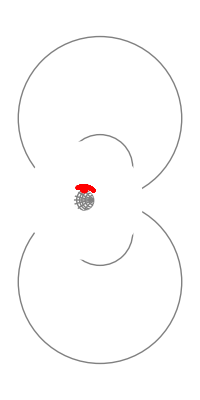

0.694115+(0.0901508+0.5003 (-0.992632+176.174 (-0.0000641145+2 δ)))/(1+2.11396×10^6 (-0.0000641145+2 δ)^2)

```mathematica
pl=ListPlot[Table[{S11RE[[a]],S11IM[[a]]},{a,1,Length[f]}],PlotStyle->{Red,Thick},PlotRange->All,AspectRatio->Automatic, AxesOrigin->{0,0}];

R1={5,10,20,30,40,60,100,300,500};
X1={10,-10,100,-100,-50,50,-25,25};
chart=Graphics[{Circle[{0,0}],Gray,Table[Circle[{1-1/(1+R1[[a]]/Z0),0},1/(1+R1[[a]]/Z0)],{a,1,Length[R1]}],Table[Circle[{1,Z0/X1[[a]]},Abs[Z0/X1[[a]]]],{a,1,Length[X1]}],Line[{{-1,0},{1,0}}],White,Thickness[0.45],Circle[{0,0},1.5]},PlotRange->1.1];
Show[chart,pl]
model
```

ⅇ^(2 Im[γ]) Abs[0.833136+(0.300251 ⅇ^(ⅈ γ))/(1+(0.+2907.89 ⅈ) δ)]^2

{γ→-0.0152443}

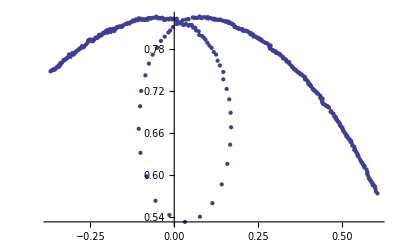

Abs[0.833136+(0.300216-0.00457694 ⅈ)/(1+(0.+2907.89 ⅈ) δ)]^2

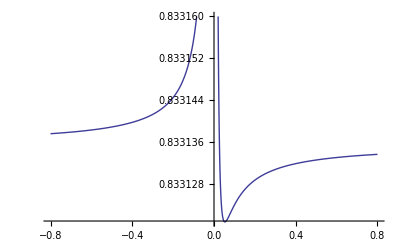

```mathematica
Γ=Abs[Exp[ⅈ (ϕ-γ)](ρ + (d Exp[ⅈγ])/(1+ⅈ QL t))]^2
Smithparam=Table[{S11RE[[x]],S11IM[[x]]},{x,1,Length[S11RE]}];

smithvar=FindFit[Smithparam,Γ,{γ},δ]
ListPlot[Smithparam]
Γ/.smithvar

Plot[(Γ)^(1/2)/.smithvar,{δ,-0.8,0.8}]
```